```mathematica
T=(m1 (l1*ϕ1'[t])^2)/2+m2 1/2((l1*ϕ1'[t])^2+(l2* ϕ2'[t])^2+2l1*l2* ϕ1'[t]* ϕ2'[t]*Cos[ϕ1[t]-ϕ2[t]]);
```

```mathematica
P=m1 g((*l1+l2*)-l1 Cos[ϕ1[t]])+m1 g((*l1+l2*)-l1 Cos[ϕ1[t]]-l2 Cos[ϕ2[t]]);
```

```mathematica
L = T - P;
```

```mathematica
eq1=D[D[L, ϕ1'[t],t]-D[L,ϕ1[t]]]==0
```

2 g l1 m1 Sin[ϕ1[t]]+l1 l2 m2 Sin[ϕ1[t]-ϕ2[t]] ϕ1'[t] ϕ2'[t]+l1^2 m1 ϕ1''[t]+1/2 m2 (-2 l1 l2 Sin[ϕ1[t]-ϕ2[t]] (ϕ1'[t]-ϕ2'[t]) ϕ2'[t]+2 l1^2 ϕ1''[t]+2 l1 l2 Cos[ϕ1[t]-ϕ2[t]] ϕ2''[t])==0

```mathematica
eq2=D[D[L, ϕ2'[t],t]-D[L,ϕ2[t]]]==0
```

g l2 m1 Sin[ϕ2[t]]-l1 l2 m2 Sin[ϕ1[t]-ϕ2[t]] ϕ1'[t] ϕ2'[t]+1/2 m2 (-2 l1 l2 Sin[ϕ1[t]-ϕ2[t]] ϕ1'[t] (ϕ1'[t]-ϕ2'[t])+2 l1 l2 Cos[ϕ1[t]-ϕ2[t]] ϕ1''[t]+2 l2^2 ϕ2''[t])==0

```mathematica
eq1Full = Assuming[{l1>0,l2>0,m1>0,m2>0}, FullSimplify[eq1]]
```

2 g m1 Sin[ϕ1[t]]+l2 m2 Sin[ϕ1[t]-ϕ2[t]] ϕ2'[t]^2+l1 (m1+m2) ϕ1''[t]+l2 m2 Cos[ϕ1[t]-ϕ2[t]] ϕ2''[t]==0

```mathematica
eq2Full = Assuming[{l1>0,l2>0,m1>0,m2>0}, FullSimplify[eq2]]
```

g m1 Sin[ϕ2[t]]+l1 m2 Cos[ϕ1[t]-ϕ2[t]] ϕ1''[t]+l2 m2 ϕ2''[t]==l1 m2 Sin[ϕ1[t]-ϕ2[t]] ϕ1'[t]^2

```mathematica
params={l1->1,l2->1,m1->1,m2->0.9,g->9.81,ϕ01->(π/1)-π/2,ϕ02->π/6};
```

```mathematica
solFull = NDSolve[{Evaluate[{eq1Full,ϕ1[0]==ϕ01,ϕ2[0]==ϕ02, ϕ1'[0]==0,
 ϕ2'[0]==0}/.params],
Evaluate[{eq2Full,ϕ1[0]==ϕ01,ϕ2[0]==ϕ02, ϕ1'[0]==0,
 ϕ2'[0]==0}/.params]},{ϕ1[t],ϕ2[t]},{t,0,30}]
```

{{ϕ1[t]→InterpolatingFunction[…][t],ϕ2[t]→InterpolatingFunction[…][t]}}

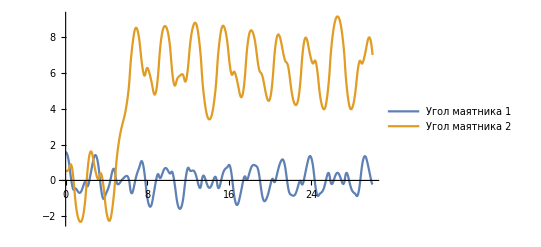

```mathematica
Plot[{ϕ1[t]/.solFull,ϕ2[t]/.solFull},{t,0,30},PlotLegends->{"Угол маятника 1","Угол маятника 2"}]
```

```mathematica
Pendulum[ϕ1_,ϕ2_]:=Module[{obj, rpend = 1},
	obj = {
(*стержень 1*)
Darker[Blue,0.1], Thickness[0.01], Line[{{0,0}, {l1*Sin[ϕ1],-l1*Cos[ϕ1]}}],
(*стержень 2*)
Darker[Green,0.1], Thickness[0.01], Line[{{l1*Sin[ϕ1],-l1*Cos[ϕ1]},{l1*Sin[ϕ1]+l2*Sin[ϕ2],-l1*Cos[ϕ1]-l2*Cos[ϕ2]}}],
(*маятник 1*)
Darker[Orange,0.1], Disk[{l1*Sin[ϕ1],-l1*Cos[ϕ1]}, 0.05],
(*маятник 2*)
Darker[Red,0.1], Disk[{l1*Sin[ϕ1]+l2*Sin[ϕ2],-l1*Cos[ϕ1]-l2*Cos[ϕ2]}, 0.05]}/.params];
```

```mathematica
Graphics[Pendulum[π/2,π/3], Frame->True, BaseStyle->16]
```

-Graphics-

```mathematica
Animate[Graphics[
Pendulum[ϕ1[t],ϕ2[t]]/.solFull/.t->ti, ImageSize->Medium, PlotRange->{{-3,3},{-3,3}}], {ti,0,30,0.05},DisplayAllSteps->True]
```